Estimate parameters of stock 000006

ⅆlog x_t=μ+θ log x_t+σⅆ W_t

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler1`";
```

```mathematica
SeedRandom[0];
```

```mathematica
csv = Import["./000006.csv","CSV"];
```

```mathematica
csv//Dimensions
```

{613,15}

```mathematica
x=Log[csv[[2;;,4]]];
```

```mathematica
UnitRootTest[x]
```

0.685684

```mathematica
y1=Drop[x,1];
y=Drop[x,-1];
```

```mathematica
K=y//Length
```

611

```mathematica
UP[θ_,μ_,σ_]:=(θ-1)^2/2+μ^2/2+σ^2/2;
```

```mathematica
f[θ_,μ_,σ_]:=Sum[1/2((y1[[i]]- μ-θ y[[i]])/σ)^2+Log[√(2 π) ]+1/2 Log[σ^2],{i,1,K}];
```

```mathematica
HessianH[f_,x_List?VectorQ]:=D[f,{x,2}]
```

```mathematica
GradientG[f_,x_List?VectorQ]:=D[f,{x,1}]
```

```mathematica
U[θ_ ,μ_,σ_]=N[Simplify[f[θ,μ,σ]+UP[θ,μ,σ]]];
```

```mathematica
dU[θ_,μ_,σ_]=Simplify[GradientG[U[θ,μ,σ],{θ,μ,σ}]];
```

```mathematica
ddU[θ_,μ_,σ_]=Simplify[HessianH[U[θ,μ,σ],{θ,μ,σ}]];
```

```mathematica
QS=hmc[U,dU,ddU,3,5000,10000,True,True];
```

501 991.109 15.7668 0.590426 0.371698 -13796.2 -12805.1 -12805.3 6.42876×10^-6 0.0156247 True {1,4,11} {1,11}

1002 990.978 0.000852651 0.607459 0.456397 -13801. -12808.1 -12810. 5.84432×10^-6 0.00970172 False {1,2,11} {1,11}

1503 987.06 18.1879 0.579951 0.343694 -13797.4 -12810.3 -12810. 7.07163×10^-6 0.0106719 True {1,4,9,10,11} {1,11}

2004 987.427 0.0019027 0.608713 0.406196 -13797.4 -12810.3 -12810. 5.31302×10^-6 0.0142043 False {1,2,3,4,11} {1,11}

2505 986.305 18.7785 0.566094 0.438562 -13798.6 -12812.3 -12811.8 7.07163×10^-6 0.00970172 True {1,2,6,10} {1,11}

3006 996.959 0.00116481 0.520781 0.388476 -13808.7 -12809.9 -12811.8 5.84432×10^-6 0.012913 False {1,3,11} {1,11}

3507 993.202 21.4928 0.577031 0.36651 -13799.5 -12806.3 -12811.8 6.42876×10^-6 0.0117391 True {1,5,7,9,11} {1,11}

4008 995.676 0.00102368 0.537044 0.420389 -13804.8 -12809.2 -12809.1 7.07163×10^-6 0.00970172 False {1,2,4,8,11} {1,11}

4509 988.55 15.8393 0.705423 0.292438 -13797.7 -12809.2 -12809.1 6.42876×10^-6 0.0117391 True {1,2,6,9,11} {1,11}

5010 992.093 0.000447847 0.686798 0.270818 -13801.5 -12809.2 -12809.4 4.83002×10^-6 0.00801795 False {1,5,11} {1,11}

5511 997.21 14.5818 0.728291 0.297721 -13806.4 -12809.2 -12809.4 4.83002×10^-6 0.00801795 True {1,5,10,11} {1,11}

6012 993.584 0.00041577 0.704863 0.378807 -13803. -12809.2 -12809.4 4.83002×10^-6 0.00801795 False {1,7,8,11} {1,11}

6513 992.725 10.9686 0.722724 0.240215 -13801.9 -12809.2 -12809.4 4.83002×10^-6 0.00801795 True {1,4,5,11} {1,11}

7014 995.432 0.000383501 0.608614 0.388587 -13804.8 -12809.2 -12809.4 4.83002×10^-6 0.00801795 False {1,10,11} {1,11}

7515 991.435 22.4431 0.647154 0.364591 -13800.6 -12809.2 -12809.4 4.83002×10^-6 0.00801795 True {1,3,8,9,11} {1,11}

8016 996.33 0.00111756 0.662651 0.383332 -13805.7 -12809.2 -12809.4 4.83002×10^-6 0.00801795 False {1,4,5,10,11} {1,11}

8517 995.393 23.3838 0.391349 0.31063 -13804.6 -12809.2 -12809.4 4.83002×10^-6 0.00801795 True {1,11} {1,11}

9018 991.327 0.000848184 0.706003 0.388998 -13800.7 -12809.2 -12809.4 4.83002×10^-6 0.00801795 False {1,8,11} {1,11}

9519 986.928 14.8136 0.731334 0.363249 -13796.1 -12809.2 -12809.4 4.83002×10^-6 0.00801795 True {1,10,11} {1,11}

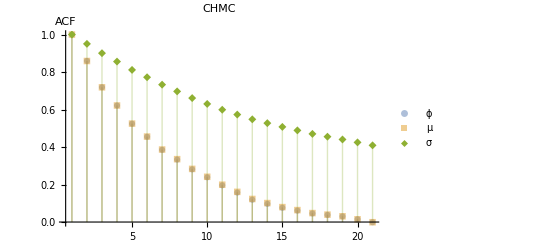

```mathematica
QS1=Table[QS[[i]],{i,1,50000,10}];
ListPlot[{CorrelationFunction[QS1[[;;,1]],{20}],CorrelationFunction[QS1[[;;,2]],{20}],CorrelationFunction[QS1[[;;,3]],{20}]},Filling->Axis,PlotRange->All,AxesLabel->{None,"ACF"},PlotLabel->CHMC,PlotLegends->{ϕ,μ,σ},PlotMarkers->Automatic,PlotStyle->{Opacity[.5],Opacity[.5],Opacity[1]}]
```

```mathematica
θ1=QS[[All,1]];
μ1=QS[[All,2]];
σ1=Abs[QS[[All,3]]];
{StandardDeviation[θ1],Mean[θ1]-3StandardDeviation[θ1],Mean[θ1]+3StandardDeviation[θ1],Mean[θ1]}
{StandardDeviation[μ1],Mean[μ1]-3StandardDeviation[μ1],Mean[μ1]+3StandardDeviation[μ1],Mean[μ1]}
{StandardDeviation[σ1],Mean[σ1]-3StandardDeviation[σ1],Mean[σ1]+3StandardDeviation[σ1],Mean[σ1]}
```

{0.00685132,0.966371,1.00748,0.986925}

{0.0119655,-0.0129863,0.0588064,0.0229101}

{0.000722648,0.0231152,0.0274511,0.0252832}

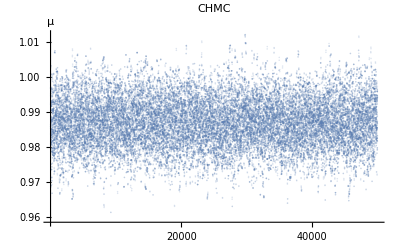

```mathematica
ListPlot[QS[[All,1]],PlotStyle->Opacity[.2],PlotLabel->"CHMC",Ticks->{{20000,40000},Automatic},AxesLabel->{None,"μ"}]
```

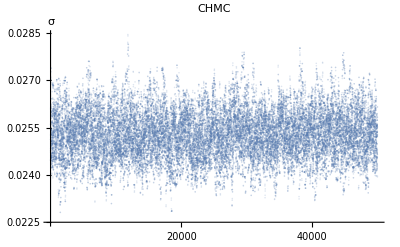

```mathematica
ListPlot[Abs[QS[[All,3]]],PlotStyle->Opacity[.2],PlotLabel->"CHMC",Ticks->{{20000,40000},Automatic},AxesLabel->{None,"σ"}]
```

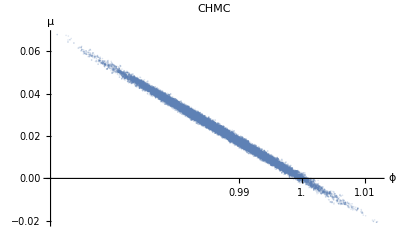

```mathematica
ListPlot[QS[[All,1;;2]],AxesLabel->{ϕ,μ},PlotLabel->"CHMC",PlotStyle->Opacity[0.2],Ticks->{{.99,1.0,1.01},Automatic}]
```

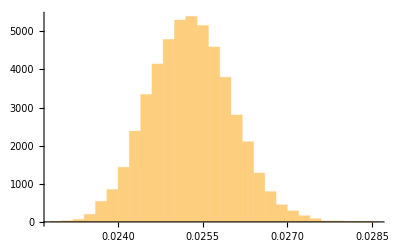

```mathematica
Histogram[Abs[QS[[All,3]]]]
```